-Graphics3D-

-Graphics3D-

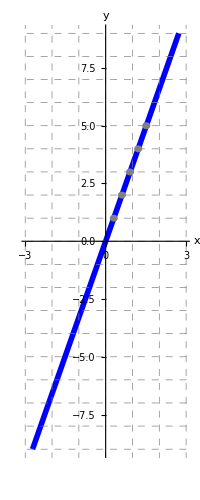

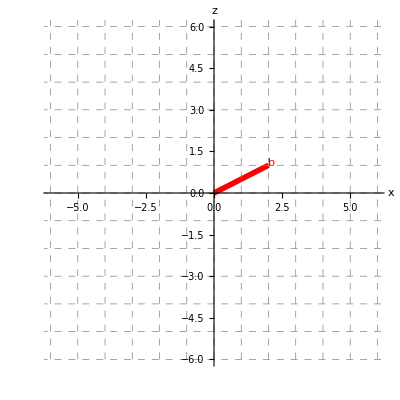

```mathematica
v = 1*{0.303023*1,1,0};
b = {2,0,1};
vVECTOR={Blue,Thickness[0.01],Arrow[{{0,0,0},v}],Style[Text["v",v+{0.1,0.1,0.1}],FontWeight->Bold,FontSize->18]};
bVECTOR={Red,Thickness[0.01],Arrow[{{0,0,0},b}],Style[Text["b",b+{0.1,0.1,0.1}],FontWeight->Bold,FontSize->18]};

Graphics3D[{vVECTOR,bVECTOR},Axes->True,FaceGrids->All,AxesOrigin->{0,0,0},AxesLabel->{Style["x",FontSize->18],Style["y",FontSize->18],Style["z",FontSize->18]},PlotRange->{{-4,4},{-4,4},{-4,4}}]
etav={Blue,Thickness[0.01],Line[{{0,0,0},5*v}]};
etavpb={Blue,Thickness[0.01],Line[{v+b,(5*v)+b}]};
metav={Blue,Thickness[0.01],Line[{{0,0,0},-5*v}]};
metavpb={Blue,Thickness[0.01],Line[{v+b,(-5*v)+b}]};
etavRIGHT={Blue,Thickness[0.01],Line[{5*v,(5*v)+b}]};
etavLEFT = {Blue,Thickness[0.01],Line[{-5*v,(-5*v)+b}]};
Graphics3D[{etav, etavpb, metav, metavpb, etavRIGHT, etavLEFT, bVECTOR},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{Style["x",FontSize->18],Style["y",FontSize->18],Style["z",FontSize->18]},PlotRange->{{-6,6},{-6,6},{-6,6}}]
v2Dxz = {v[[1]],v[[2]]};
b2Dxy = {b[[1]],b[[3]]};
etav2Dxz={Blue,Thickness[0.01],Line[{{0,0},9*v2Dxz}]};
metav2Dxz={Blue,Thickness[0.01],Line[{{0,0},-9*v2Dxz}]};
vUNIT={Gray,Thickness[0.005], Disk[v2Dxz,0.15],Disk[2*v2Dxz,0.15],Disk[3*v2Dxz,0.15],Disk[4*v2Dxz,0.15],Disk[5*v2Dxz,0.15] ,Style[FontWeight->Bold,FontSize->18]};
bVECTOR2Dxy={Red,Thickness[0.01],Line[{{0,0},b2Dxy}],Style[Text["b",b2Dxy+{0.1,0.1}],FontWeight->Bold,FontSize->18]};
Graphics[{etav2Dxz, metav2Dxz, vUNIT},Axes->True,AxesOrigin->{0,0},AxesLabel->{Style["x",FontSize->18],Style["y",FontSize->18]},PlotRange->{{-3,3},{-9,9}},GridLines->{Range[-11,11],Range[-11,11]},GridLinesStyle->Directive[Gray,Dashed]]
Graphics[{bVECTOR2Dxy},Axes->True,AxesOrigin->{0,0},AxesLabel->{Style["x",FontSize->18],Style["z",FontSize->18]},PlotRange->{{-6,6},{-6,6}},GridLines->{Range[-11,11],Range[-11,11]},GridLinesStyle->Directive[Gray,Dashed]]
```